```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"};
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"};

If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]

Get["ImageModeling.m"]
```

```mathematica
dim=2^8
min=-3;
max=3;
```

256

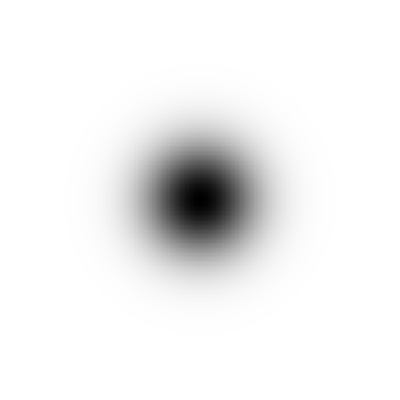

{256,256}

```mathematica
targetArrayGauss=Table[Exp[-(x^2+y^2)],{x,min,max,(max-min)/(dim-1)},{y,min,max,(max-min)/(dim-1)}];
ArrayPlot[%]
Dimensions@targetArrayDot
```

```mathematica
(targetArrayDot=Table[Boole[x^2+y^2≤((max-min)/8)^2],{x,min,max,(max-min)/(dim-1)},{y,min,max,(max-min)/(dim-1)}]);
ArrayPlot[%]
Dimensions@targetArrayDot
```

-Graphics-

{256,256}

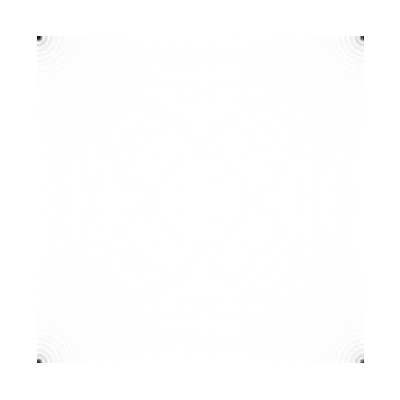

```mathematica
ArrayPlot@Fourier[targetArrayDot,FourierParameters->{1,1}]
```

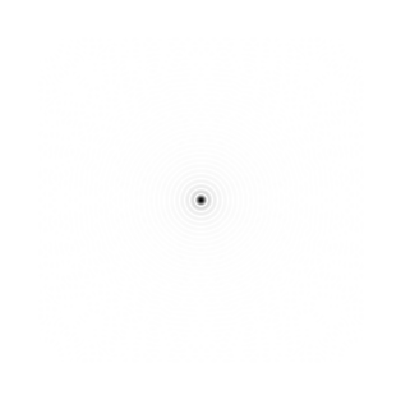

```mathematica
ArrayPlot@Abs@Transpose[RotateLeft[Transpose[RotateLeft[Fourier@targetArrayDot,dim/2]],dim/2]]
```

```mathematica
ArrayPlot@Abs@Transpose[RotateLeft[Transpose[RotateLeft[Fourier@targetArrayGauss,dim/2]],dim/2]]
```

-Graphics-

```mathematica
ArrayPlot@Abs@InverseFourier@Fourier@targetArrayGauss
```

-Graphics-

```mathematica
ArrayPlot@Abs@rearrange2DFourierArray@Fourier@targetArrayDot
```

-Graphics-